# Riemann Integration

## Setup

Choose a function to integrate:

```mathematica
f[x_]:= Sin[x];
```

Select a lower and upper bound

```mathematica
lowerBound = 0;
upperBound = π;
```

Choose the number of steps to use

```mathematica
numSteps = 100;
```

## Integration Algorithm

Calculate the width of each rectangle, or what we might refer to as the "stepsize". Computational Scientists usually call this quantity h.

```mathematica
h =(upperBound - lowerBound)/numSteps;
```

Calculate the area of each rectangle in one simple step:

```mathematica
rectangleSizes = Table[N[f[h i] *h],{i,0,numSteps -1}];
```

Sum the rectangles to get the Total area for the region in question

```mathematica
approximateAreaUnderCurve = Total[rectangleSizes]
```

1.99984

## Analysis of Error

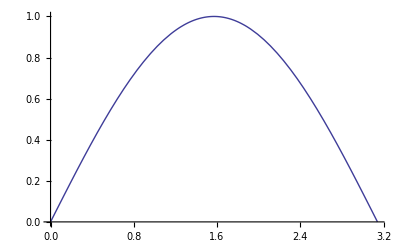

```mathematica
Plot[f[x],{x,lowerBound,upperBound}]
```

```mathematica
analyticValue=∫_lowerBound^upperBound f[x]ⅆx
```

2

```mathematica
Abs[analyticValue - approximateAreaUnderCurve]
```

0.000164496